## Intro/Functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Units

Units are in m unless otherwise specified.

```mathematica
inches = 25.4/1000;
mm = 1/1000;
```

### Functions

This function finds the reflection of a ray with the optic. Optic is assumed to have values in Optic[“Surface”], Optic[“Direction”], Optic[“Center”], Optic[“SurfaceNormal”] and Optic[“Region”]. Returns false if does not intersect within the region, otherwise returns a ray and a bragg angle. Rays consist of a position and a unit direction vector. This is only 25% faster than the previous ReflectOptic. Probably due to the stupidly complicated solution. An idea would be to solve it by hand but that doesn’t work for an arbitrary function. Taylor series?

```mathematica
ReflectOptic[Optic_,Ray_]:=Module[{int,ref,bragg},
int = Optic["Solution"]@@Ray;
If[!(int[[{1,3}]]∈Optic["Region"]),
Return[False]];
ref=Ray[[2]]-2*Ray[[2]].Optic["SurfaceNormal"][{int[[1]],int[[3]]}]Optic["SurfaceNormal"][{int[[1]],int[[3]]}];
bragg =ArcCos[ref.Ray[[2]]]/2;
{{int,ref},bragg}
]
```

Gives the intersection of a ray with the detector plane. The detector has to have values in Detector[“Position”], Detector[“Normal”], and Detector[“Transform”]. Coordinates are given in local coordinates.

```mathematica
IntersectDetector[Detector_,Ray_]:=Module[{line, t,x,y,z, plane,sol,int},
line =(Ray[[1]]+t*Ray[[2]]=={x,y,z});
plane = (({x,y,z}-Detector["Position"]).Detector["Normal"] == 0);
sol = NSolve[plane&&line,{x,y,z,t}][[1]];
int = {x,y,z}/.sol;
Detector["Transform"][int]
]
```

Creates a list of colors from red to blue

```mathematica
Colors[n_]:=ColorData["DarkRainbow"][(n-#)/(n-1)]&/@Range[n]
```

```mathematica
Colors[10]
```

{RGBColor[0.72987, 0.239399, 0.230961],RGBColor[0.7390852222222222, 0.2704317777777778, 0.23901633333333333],RGBColor[0.8272665555555555, 0.5658831111111111, 0.3086672222222222],RGBColor[0.8562609999999999, 0.742794, 0.31908333333333333],RGBColor[0.7294032222222222, 0.7249631111111111, 0.2860526666666667],RGBColor[0.5090482222222222, 0.6077703333333333, 0.25180933333333333],RGBColor[0.33311066666666667, 0.5032283333333333, 0.26154733333333335],RGBColor[0.2704347777777778, 0.43505644444444447, 0.35968022222222223],RGBColor[0.2548481111111111, 0.35357422222222223, 0.5389008888888889],RGBColor[0.237736, 0.340215, 0.575113]}

Helper function for NMinimize so that it will ignore imaginary values.

```mathematica
Realify[value_]:=Re[value]+1000000*Abs[Im[value]]
```

## Geometry

### Constants

Descriptions:
RowlandR - Radius of the rowland circle
Bragg - Bragg angle you are working at in radians. 90 degrees is backscatter.
NRays is the number of rays to simulate with. ~25% will miss the optic currently.
opticR - Radius of a cicular optic (not bend radius)
opticBend - Bend radius of an optic (Ideally 2 * RowlandR)
toroidalAngle - Bragg angle for which the toroidal optic is designed. For spherical, use 90 degrees.
sourceSize - Size of the source in each dimension. Assumed to be a box centered on the rowland circle. NOT IMPLEMENTED
sourceAngle - θ-angle between the x-z plane of the source and the line from the source to the optic. Note: Only theta angle supported so far. NOT IMPLEMENTED

```mathematica
RowlandR = 0.5;
Bragg =85 Degree;
NRays = 3000;
opticR = 2 inches;
opticBend =2RowlandR;
toroidalAngle =70 Degree;
sourceSize = {10 mm, 0, 1 mm};
sourceAngle = 6 Degree;
detectorArea= 25 mm^2;
```

### Components

Here we define the positions and properties of the components of the monochromator.

#### Optic

Position is the center of the wafer.
Direction is the normal vector to the optic from that position.
Center is the center of curvature of the optic.
TorusRadius is the minor radius for the torus. For spherical, this will be zero.
Region is the x,z region the optic takes up.
Eqn is the equation y(x,z) of the torus (or sphere) of the optic. It is assumed that y is positive to make this single valued. For very different setups, this will have to be changed.
Surface is the function f(x,y,z) such that f(x,y,z) = 0 is the equation for our torus.
SurfaceNormal is the normal vector at any point (x,z) on the optic. Useful for the reflection.
Depth is the distance from the front of the optic to the deepest point of the optic.
Solution is the solution {x,y,z} of intersecting Optic[“Surface”] = 0 with any line going through {x0,y0,z0} in the direction {lx,ly,lz}. It works by finding the solution which is closest to Optic[“Position”], so this may not work in pathological examples.
	Solution is a wrapper function for Sol which needs to have no arguments and be evaluated when that cell is run. The arguments it needs are protected so you will not be able to edit x0,y0,z0,lx,ly,lz.

```mathematica
Clear[Optic];
Optic["Position"] = {0,RowlandR,0};
Optic["Direction"] = {0,-1,0};
Optic["Center"] = Optic["Position"]+Optic["Direction"]*opticBend;
Optic["TorusRadius"] = opticBend Cos[toroidalAngle]^2;
Optic["TorusCenter"] = Optic["Center"]-Optic["Direction"]*(Optic["TorusRadius"]);
Optic["Region"] = Disk[{0,0},opticR];
Optic["OpeningAngle"] = ArcSin[opticR/opticBend];
Optic["Eqn"][x_,z_]:=((-(z-Optic["TorusCenter"][[3]])^2+(Optic["TorusRadius"]-(opticBend^2-(x-Optic["TorusCenter"][[1]])^2)^0.5)^2)^0.5+Optic["TorusCenter"][[2]])
Optic["Surface"][{x_,y_,z_}]:=y-Optic["Eqn"][x,z]
Optic["SurfaceNormal"][{x1_,z1_}]:=Module[{x,y,z,eqn,norm},
eqn = -Grad[Optic["Surface"][{x,y,z}],{x,y,z}];
norm =eqn/.{x->x1,y->Optic["Eqn"][x1,z1],z->z1};
norm/Norm[norm]
]
Unprotect[x1,z1];
Clear[x1,z1];
Protect[x1,z1];
Optic["Series"]=Normal[Series[Optic["Eqn"][x1-Optic["Center"][[1]],z1-Optic["Center"][[3]]],{x1,0,4},{z1,0,4}]];
Optic["Appx"][x_,z_]:=Optic["Series"]/.{x1->x+Optic["Center"][[1]],z1->z+Optic["Center"][[3]]}
Unprotect[x0,lx,y0,ly,z0,lz];
Clear[x0,lx,y0,ly,z0,lz]
Protect[x0,lx,y0,ly,z0,lz];
Optic["Sol"]=Module[{line,sol,x,y,z,t,index,ints},
line = {x->x0+lx t,y->y0+ly t,z->z0+lz t};
sol = NSolve[Optic["Appx"][x,z]==y/.line,t,Method->"Homotopy"];
ints = {x,y,z}/.(line/.sol);
index = Ordering[Norm[Optic["Position"]-#]&/@(ints/.
{x0->Optic["Position"][[1]],y0->Optic["Position"][[2]],z0->Optic["Position"][[3]],lx->-Optic["Direction"][[1]],ly->-Optic["Direction"][[2]],lz->-Optic["Direction"][[2]]}),1][[1]];
ints[[index]]
];
Optic["Solution"][pos_,dir_]:=Optic["Sol"]/.{x0->pos[[1]],y0->pos[[2]],z0->pos[[3]],lx->dir[[1]],ly->dir[[2]],lz->dir[[3]]}
Optic["Depth"] = NMaximize[Realify[Optic["Eqn"][x,z]],{x,z}∈Optic["Region"]][[1]]-NMinimize[Realify[Optic["Eqn"][x,z]],{x,z}∈Optic["Region"]][[1]];
```

Root::deg: 0.+1.11169×10^47 #1+6.29479×10^46 #1^2+2.01826×10^46 #1^4 has fewer than 5 root(s) as a polynomial in #1.

General::stop: Further output of Root::deg will be suppressed during this calculation.

```mathematica
Plot3D[Optic["Eqn"][x,z]-Optic["Appx"][x,z],{x,z}∈Optic["Region"]]
```

-Graphics3D-

```mathematica
Timing[ReflectOptic[Optic,#]&/@rays;][[1]]
```

7.57813

```mathematica
TableForm[{{"∞ (Torus)",xinf},{"6",x6},{"4",x4},{"2",x2}},TableHeadings->{None,{"Degree","Time (s)"}}]
```

Degree | Time (s)
∞ (Torus) | 39.1094
6 | 15.2188
4 | 5.45313
2 | 19.4688

```mathematica
Plot3D[Optic["Eqn"][x,z],{x,z}∈Optic["Region"],PlotRange->All]
```

-Graphics3D-

#### Source

Position is the center of the source.
Direction is the direction from the source to the optic.
Rotation is the rotation matrix from the source coordinates to the global coordinates.
Transform is a function which translates from local source coordinates to the global coordinates.

```mathematica
Clear[Source]
Source["Position"]={RowlandR*Sin[2(Pi/2-Bragg)],-RowlandR*Cos[2(Pi/2-Bragg )],0};
Source["Direction"] =(Optic["Position"]-Source["Position"])/((Optic["Position"]-Source["Position"]).(Optic["Position"]-Source["Position"]))^0.5;
Source["Rotation"] = Module[{rotAngle},
rotAngle = Pi-Bragg+sourceAngle;
RotationMatrix[rotAngle,{0,0,1}]
];
Source["Transform"][xVector_]:=Source["Rotation"].xVector+Source["Position"];
```

#### Detector

Position is the center of the detector.
Direction is the direction from the detector to the optic.
Rotation is the rotation matrix from the global coordinates to the local detector coordinates (x,z).
Transform transforms from global coordinates to the local detector coordinates.

```mathematica
Detector["Position"]= {-RowlandR*Sin[2(Pi/2-Bragg )],-RowlandR*Cos[2(Pi/2-Bragg )],0};
Detector["Normal"] = (Optic["Position"]-Detector["Position"])/((Optic["Position"]-Detector["Position"]).(Optic["Position"]-Detector["Position"]))^0.5;
Detector["Rotation"] = {{1,0,0},{0,0,1},{0,1,0}}.RotationMatrix[{Detector["Normal"],{0,1,0}}];
Detector["Transform"][xVector_] := Detector["Rotation"].(xVector - Detector["Position"]); 
Detector["Radius"] = (detectorArea/Pi)^0.5;
```

### Math

Plot the Rowland circle. Optic is in red.

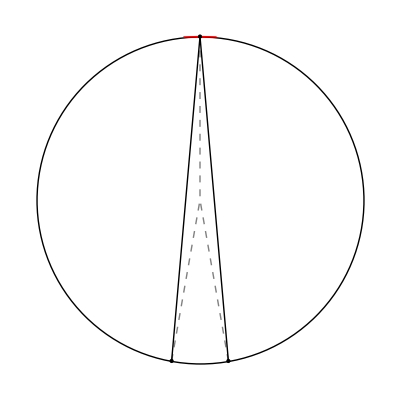

```mathematica
Graphics[{
{Gray,Dashed,Line[{Optic["Position"][[{1,2}]],{0,0}}]},
{Gray,Dashed,Line[{Source["Position"][[{1,2}]],{0,0}}]},
{Gray,Dashed,Line[{Detector["Position"][[{1,2}]],{0,0}}]},
{Thick,Line[{Optic["Position"][[{1,2}]],Source["Position"][[{1,2}]]}]},
{Thick,Line[{Optic["Position"][[{1,2}]],Detector["Position"][[{1,2}]]}]},
{Circle[{0,0},RowlandR]},
{Red,Circle[{0,Optic["Position"][[2]]-opticBend},opticBend,{Pi/2-Optic["OpeningAngle"],Pi/2+Optic["OpeningAngle"]}]},
{Point[{Optic["Position"][[{1,2}]],Source["Position"][[{1,2}]],Detector["Position"][[{1,2}]]}]}
}
]
```

Here we find a range of theta, phi angles from the source which include the whole optic. Needs to be changed for finite source.

```mathematica
thetaMax =ArcTan[(Optic["Position"][[1]]-Source["Position"][[1]]-opticR),(Optic["Position"][[2]]-Source["Position"][[2]]- Optic["Depth"])];
thetaMin = ArcTan[(Optic["Position"][[1]]-Source["Position"][[1]]+opticR),(Optic["Position"][[2]]-Source["Position"][[2]]-Optic["Depth"])];
phiMin =Pi/2+ 1.05ArcTan[-opticR/((Optic["Position"][[1]]-Source["Position"][[1]])^2+(Optic["Position"][[2]]-Source["Position"][[2]]-Optic["Depth"])^2)^0.5];
phiMax =Pi/2+ 1.05ArcTan[opticR/((Optic["Position"][[1]]-Source["Position"][[1]])^2+(Optic["Position"][[2]]-Source["Position"][[2]]-Optic["Depth"])^2)^0.5];
```

```mathematica
phis = RandomReal[{phiMin,phiMax},NRays];
thetas = RandomReal[{thetaMin,thetaMax},NRays];
angles = Transpose[{thetas,phis}];
directions = {Cos[thetas[[#]]]Sin[phis[[#]]],Sin[thetas[[#]]]Sin[phis[[#]]],Cos[phis[[#]]]}&/@Range[NRays];
(* Change following for finite source *)
sourcepts = Source["Position"]&/@Range[NRays];
rays = Transpose[{sourcepts,directions}];
```

```mathematica
pts = Point/@(#-{180-Bragg/Degree,90}&/@(angles/Degree));
refs = ReflectOptic[Optic,#]&/@rays;
angleplot = {If[refs[[#]]===False,Red,Blue],pts[[#]]}&/@Range[Length[pts]];
```

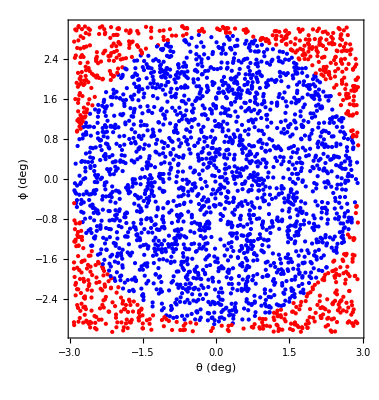

```mathematica
Graphics[angleplot,Frame->True,FrameLabel->{"θ (deg)","ϕ (deg)"},LabelStyle->16]
```

```mathematica
validRays = Cases[refs,_?(#=!=False&)];
```

```mathematica
Length[validRays]
```

2248

```mathematica
maxBragg = Max[validRays[[;;,2]]];
minBragg = Min[validRays[[;;,2]]];
colorBragg[Bragg_]:=ColorData["DarkRainbow"][(Bragg-minBragg)/(maxBragg-minBragg)]
```

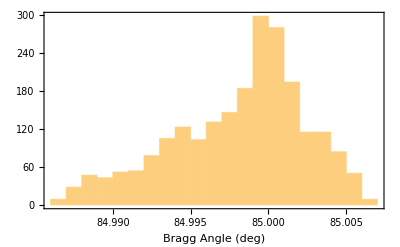

```mathematica
BHist[toroidalAngle,Bragg]=Histogram[validRays[[;;,2]]/Degree,Frame->{{True,False},{True,False}}, FrameLabel->{"Bragg Angle (deg)",None}]
```

Finally, we plot the output as a function of detector position.

```mathematica
detectorPos = IntersectDetector[Detector,#]&/@validRays[[;;,1]];
```

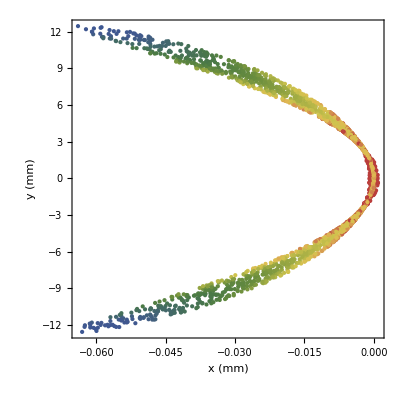

```mathematica
plots[toroidalAngle,Bragg]=Graphics[{
{colorBragg[validRays[[#,2]]],Point[detectorPos[[#,{1,2}]]/mm]}&/@Range[Length[validRays]]
},Frame->True,AspectRatio->1,LabelStyle->14,FrameLabel->{"x (mm)","y (mm)"}]
```

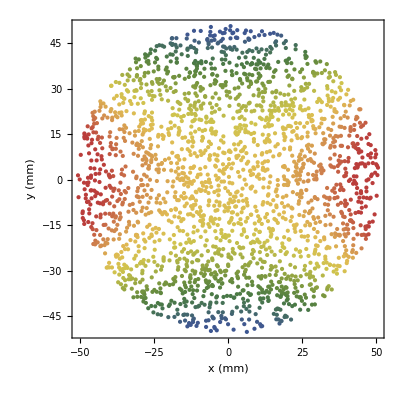

```mathematica
SBCAPlot[toroidalAngle,Bragg]=Graphics[{
{colorBragg[validRays[[#,2]]],Point[validRays[[#,1,1,{1,3}]]/mm]}&/@Range[Length[validRays]]
},Frame->True,AspectRatio->1,LabelStyle->14,FrameLabel->{"x (mm)","y (mm)"}]
```

```mathematica
Clear[DoMath]
Options[DoMath] = {verbose->False,nRays->NRays,dSize->Automatic};
DoMath[toroidalAngle_,Bragg_,opts:OptionsPattern[]]:=Module[{θ,Optic,Source,Detector,thetaMax,thetaMin,phiMax,phiMin,phis,thetas,angles,directions,sourcepts,rays,pts,refs,angleplot,validRays,maxBragg,minBragg,colorBragg,detectorPos},

If[OptionValue[verbose]==="Only"||OptionValue[verbose],Print["Toroidal Angle: "<>ToString[toroidalAngle/Degree//N]<>"°    Bragg Angle: "<>ToString[Bragg/Degree//N]<>"°"];];

Optic["Position"] = {0,RowlandR,0};
Optic["Direction"] = {0,-1,0};
Optic["Center"] = Optic["Position"]+Optic["Direction"]*opticBend;
Optic["TorusRadius"] = opticBend Cos[toroidalAngle]^2;
Optic["TorusCenter"] = Optic["Center"]-Optic["Direction"]*(Optic["TorusRadius"]);
Optic["OpeningAngle"] = ArcSin[opticR/opticBend];
Optic["Eqn"][x_,z_]:=((-(z-Optic["TorusCenter"][[3]])^2+(Optic["TorusRadius"]-(opticBend^2-(x-Optic["TorusCenter"][[1]])^2)^0.5)^2)^0.5+Optic["TorusCenter"][[2]]);
Optic["Surface"][{x_,y_,z_}]:=y-Optic["Eqn"][x,z];
Optic["SurfaceNormal"][{x1_,z1_}]:=Module[{x,y,z,eqn,norm},
eqn = -Grad[Optic["Surface"][{x,y,z}],{x,y,z}];
norm =eqn/.{x->x1,y->Optic["Eqn"][x1,z1],z->z1};
norm/(norm.norm)^0.5
];
Optic["Depth"] =Optic["Position"][[2]]- NMinimize[{Optic["Eqn"][opticR Cos[θ],opticR Sin[θ]],0≤ θ≤ 2 Pi},θ][[1]];

Source["Position"]={RowlandR*Sin[2(Pi/2-Bragg)],-RowlandR*Cos[2(Pi/2-Bragg )],0};
Source["Direction"] =(Optic["Position"]-Source["Position"])/((Optic["Position"]-Source["Position"]).(Optic["Position"]-Source["Position"]))^0.5;
Source["Rotation"] = Module[{rotAngle},
rotAngle = Pi-Bragg+sourceAngle;
RotationMatrix[rotAngle,{0,0,1}]
];
Source["Transform"][xVector_]:=Source["Rotation"].xVector+Source["Position"];

Detector["Position"]= {-RowlandR*Sin[2(Pi/2-Bragg )],-RowlandR*Cos[2(Pi/2-Bragg )],0};
Detector["Normal"] = (Optic["Position"]-Detector["Position"])/((Optic["Position"]-Detector["Position"]).(Optic["Position"]-Detector["Position"]))^0.5;
Detector["Rotation"] = {{1,0,0},{0,0,1},{0,1,0}}.RotationMatrix[{Detector["Normal"],{0,1,0}}];
Detector["Transform"][xVector_] := Detector["Rotation"].(xVector - Detector["Position"]); 
If[OptionValue[dSize]===Automatic,Detector["Radius"] = (detectorArea/Pi)^0.5,Detector["Radius"]=dSize];

If[OptionValue[verbose],
 Print["Diagram"];
Print[Graphics[{
{Gray,Dashed,Line[{Optic["Position"][[{1,2}]],{0,0}}]},
{Gray,Dashed,Line[{Source["Position"][[{1,2}]],{0,0}}]},
{Gray,Dashed,Line[{Detector["Position"][[{1,2}]],{0,0}}]},
{Thick,Line[{Optic["Position"][[{1,2}]],Source["Position"][[{1,2}]]}]},
{Thick,Line[{Optic["Position"][[{1,2}]],Detector["Position"][[{1,2}]]}]},
{Circle[{0,0},RowlandR]},
{Red,Circle[{0,Optic["Position"][[2]]-opticBend},opticBend,{Pi/2-Optic["OpeningAngle"],Pi/2+Optic["OpeningAngle"]}]},
{Point[{Optic["Position"][[{1,2}]],Source["Position"][[{1,2}]],Detector["Position"][[{1,2}]]}]}
}
]]];

thetaMax =ArcTan[(Optic["Position"][[1]]-Source["Position"][[1]]-opticR),(Optic["Position"][[2]]-Source["Position"][[2]]- Optic["Depth"])];
thetaMin = ArcTan[(Optic["Position"][[1]]-Source["Position"][[1]]+opticR),(Optic["Position"][[2]]-Source["Position"][[2]]-Optic["Depth"])];
phiMin =Pi/2+ 1.05ArcTan[-opticR/((Optic["Position"][[1]]-Source["Position"][[1]])^2+(Optic["Position"][[2]]-Source["Position"][[2]]-Optic["Depth"])^2)^0.5];
phiMax =Pi/2+ 1.05ArcTan[opticR/((Optic["Position"][[1]]-Source["Position"][[1]])^2+(Optic["Position"][[2]]-Source["Position"][[2]]-Optic["Depth"])^2)^0.5];

phis = RandomReal[{phiMin,phiMax},OptionValue[nRays]];
thetas = RandomReal[{thetaMin,thetaMax},OptionValue[nRays]];
angles = Transpose[{thetas,phis}];
directions = {Cos[thetas[[#]]]Sin[phis[[#]]],Sin[thetas[[#]]]Sin[phis[[#]]],Cos[phis[[#]]]}&/@Range[OptionValue[nRays]];
(* Change following for finite source *)
sourcepts = Source["Position"]&/@Range[OptionValue[nRays]];
rays = Transpose[{sourcepts,directions}];

pts = Point/@(#-{180-Bragg/Degree,90}&/@(angles/Degree));
refs = ReflectOptic[Optic,#]&/@rays;
angleplot = {If[refs[[#]]===False,Red,Blue],pts[[#]]}&/@Range[Length[pts]];

If[OptionValue[verbose],
 Print["Intersecting Rays Plot:"];
Print[Graphics[angleplot,Frame->True,FrameLabel->{"θ (deg)","ϕ (deg)"},LabelStyle->16]]];

validRays = Cases[refs,_?(#=!=False&)];
If[OptionValue[verbose],
Print["Rays hitting the optic: "ToString[N[Length[validRays]/OptionValue[nRays]*100]]<>"%"]];

maxBragg = Max[validRays[[;;,2]]];
minBragg = Min[validRays[[;;,2]]];
colorBragg[B_]:=ColorData["DarkRainbow"][(B-minBragg)/(maxBragg-minBragg)];

BHist[toroidalAngle,Bragg]=Histogram[validRays[[;;,2]]/Degree,Frame->{{True,False},{True,False}}, FrameLabel->{"Bragg Angle (deg)",None}];
If[OptionValue[verbose],
Print["Bragg Histogram"];
Print[BHist[toroidalAngle,Bragg]]];

detectorPos = IntersectDetector[Detector,#]&/@validRays[[;;,1]];

plots[toroidalAngle,Bragg]=Graphics[{
{colorBragg[validRays[[#,2]]],Point[detectorPos[[#,{1,2}]]/mm]}&/@Range[Length[validRays]],
(*{Opacity[0.2],Darker[Gray],Disk[{0,0},Detector["Radius"]/mm]}*)
},Frame->True,AspectRatio->1,LabelStyle->14,FrameLabel->{"x (mm)","y (mm)"}];

If[OptionValue[verbose],
Print["Detector Plot:"];
Print[plots[toroidalAngle,Bragg]]];

SBCAPlot[toroidalAngle,Bragg]=Graphics[{
{colorBragg[validRays[[#,2]]],Point[validRays[[#,1,1,{1,3}]]/mm]}&/@Range[Length[validRays]]
},Frame->True,AspectRatio->1,LabelStyle->14,FrameLabel->{"x (mm)","y (mm)"}];

If[OptionValue[verbose],
Print["SBCA Plot:"];
Print[SBCAPlot[toroidalAngle,Bragg]]];

heights[toroidalAngle,Bragg] = Max[detectorPos[[;;,2]]]-Min[detectorPos[[;;,2]]];
If[OptionValue[verbose],
Print["Height at detector: "<>ToString[heights[toroidalAngle,Bragg]]]];

widths[toroidalAngle,Bragg] =  Max[detectorPos[[;;,1]]]-Min[detectorPos[[;;,1]]];
If[OptionValue[verbose],
Print["Width at detector: "<>ToString[widths[toroidalAngle,Bragg]]]];

detectorFraction[toroidalAngle,Bragg] = Length[Cases[detectorPos[[;;,{1,2}]],_?(#.#≤Detector["Radius"]^2&)]]/Length[validRays];
If[OptionValue[verbose],
Print["Detector Collection Efficiency: "<>ToString[detectorFraction[toroidalAngle,Bragg]*100//N]<>"%"]];

VHist[toroidalAngle,Bragg]=Histogram[detectorPos[[;;,2]]/mm,Frame->{{True,False},{True,False}}, FrameLabel->{"Y position (mm)",None}];
If[OptionValue[verbose],
Print["Vertical Histogram:"];
Print[VHist[toroidalAngle,Bragg]]];

]
```

Toroidal Angle: 90.°    Bragg Angle: 75.°

Diagram

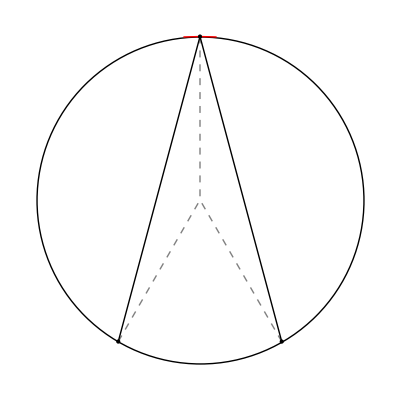

Intersecting Rays Plot:

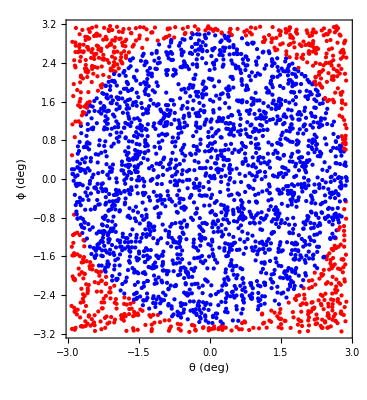

74.5% Rays hitting the optic:

Bragg Histogram

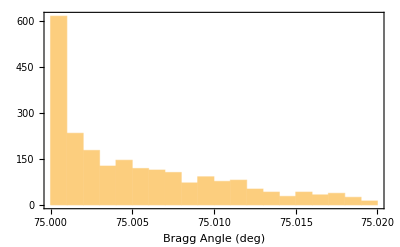

Detector Plot:

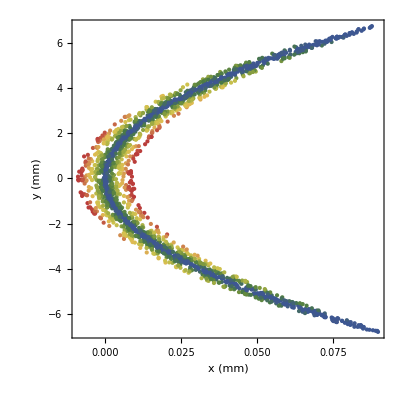

SBCA Plot:

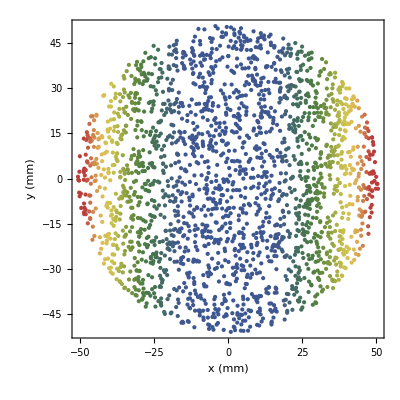

Height at detector: 0.0135738

Width at detector: 0.0000985944

Detector Collection Efficiency: 51.7673%

Vertical Histogram:

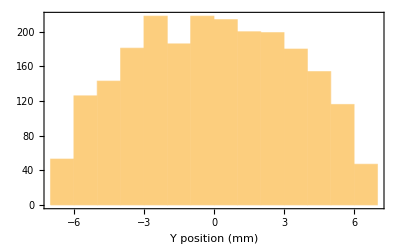

```mathematica
DoMath[90Degree,75Degree,verbose->True]
```

```mathematica
DoMath[75 Degree,# Degree,nRays->3000,verbose->"Only"]&/@{69,70,71,79,80,81};
```

Toroidal Angle: 75.°    Bragg Angle: 69.°

Toroidal Angle: 75.°    Bragg Angle: 70.°

Toroidal Angle: 75.°    Bragg Angle: 71.°

Toroidal Angle: 75.°    Bragg Angle: 79.°

Toroidal Angle: 75.°    Bragg Angle: 80.°

Toroidal Angle: 75.°    Bragg Angle: 81.°

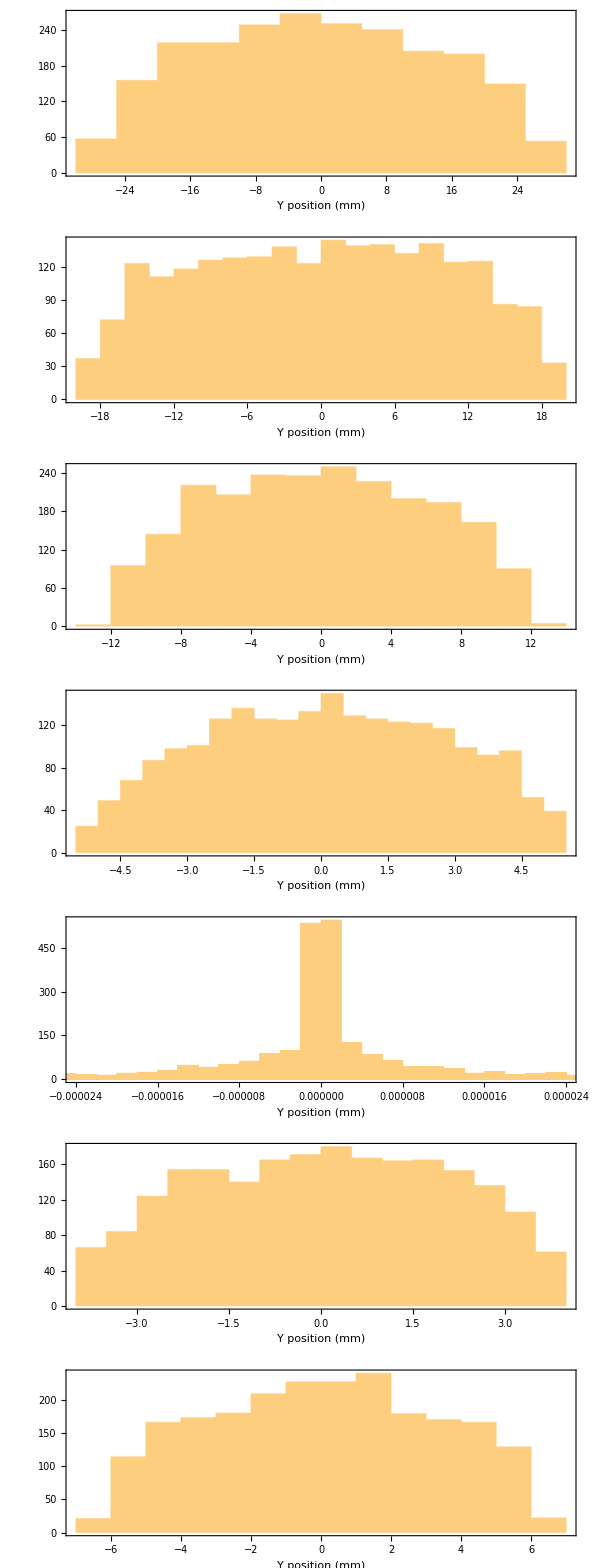

```mathematica
GraphicsGrid[Table[{VHist[75 Degree, bragg Degree]},{bragg,55,85,5}],ImageSize->600]
```

```mathematica
Export["Vdist75.png",%]
```

Vdist75.png

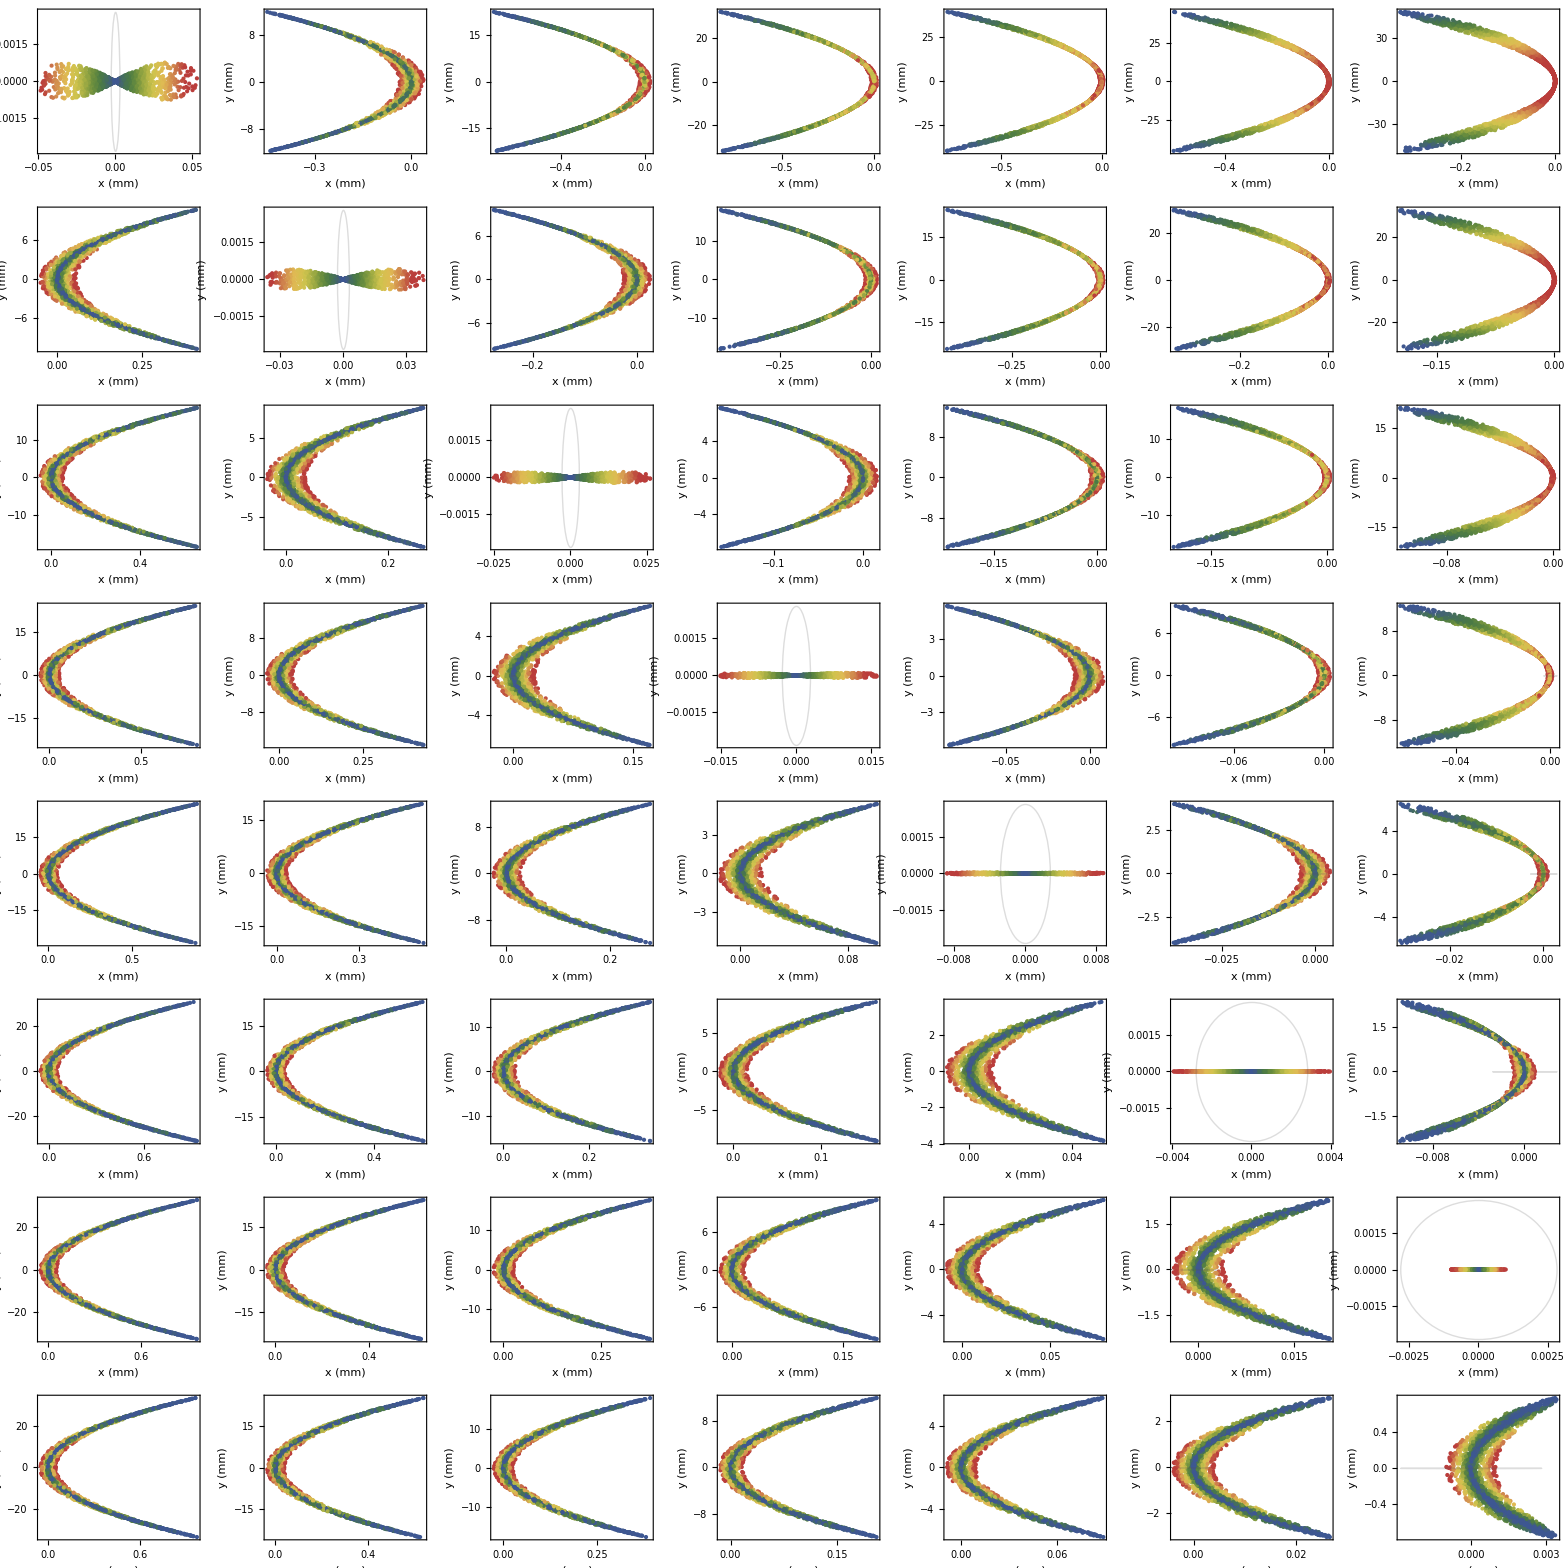

```mathematica
GraphicsGrid[Table[plots[tor Degree,bragg Degree],{tor,55,90,5},{bragg,55,85,5}],ImageSize->2400]
```

```mathematica
Export["Detector Plots.png", %]
```

Detector Plots.png

```mathematica
t=Table[detectorFraction[tor Degree,bragg Degree],{tor,55,90,5},{bragg,55,85,5}]//N
```

{{1.,0.31605,0.168365,0.118333,0.0862921,0.0729443,0.067706},{0.318681,1.,0.363273,0.214732,0.146865,0.117138,0.108145},{0.200712,0.398032,1.,0.455267,0.244087,0.182382,0.165014},{0.147722,0.240161,0.481949,1.,0.591755,0.359453,0.290621},{0.127773,0.175056,0.296214,0.617937,1.,0.825815,0.560484},{0.119058,0.152203,0.241349,0.379401,0.834729,1.,1.},{0.108191,0.145126,0.199038,0.316867,0.575744,1.,1.},{0.107064,0.137083,0.207753,0.293363,0.515869,0.970483,1.}}

```mathematica
BAngs = Range[55,85,5];
TAngs = Range[55,90,5];
```

```mathematica
Labelled = Transpose[{BAngs&/@t,t},{3,1,2}];
```

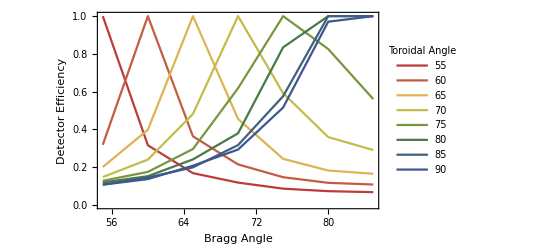

```mathematica
ListPlot[Labelled,PlotLegends->LineLegend[TAngs,LegendLabel->"Toroidal Angle"],Joined->True,Frame->True,FrameLabel->{"Bragg Angle", "Detector Efficiency"},LabelStyle->16,PlotStyle->Colors[Length[Labelled]]]
```

```mathematica
Export["EfficiencyPlot.png",%];
```

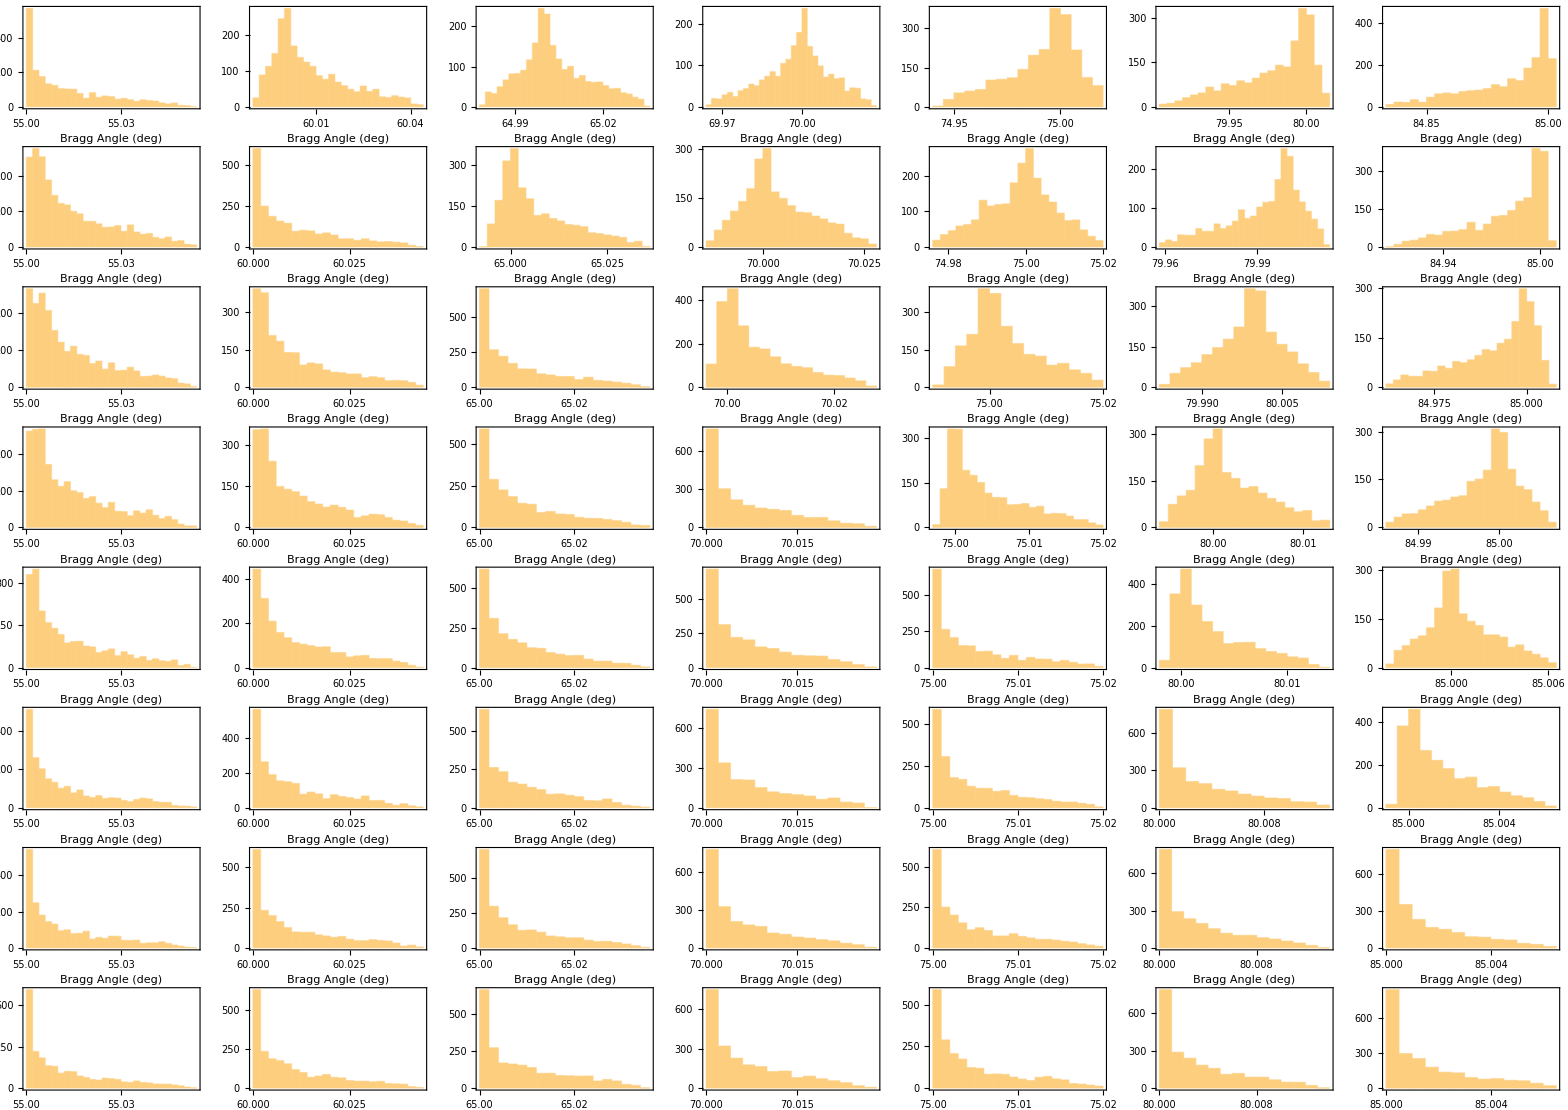

```mathematica
GraphicsGrid[Table[BHist[tor Degree,bragg Degree],{tor,55,90,5},{bragg,55,85,5}],ImageSize->2400]
```

```mathematica
Export["Histograms.png",%]
```

Histograms.png

```mathematica
t=(Table[heights[tor Degree,bragg Degree],{tor,55,90,5},{bragg,55,85,5}]/mm)//N
```

{{0.00150066,23.7061,45.0788,63.7895,78.8571,90.3944,97.2371},{21.2346,0.000825757,19.2758,35.87,49.4931,59.3502,65.3901},{36.9937,17.5389,0.000436278,15.1604,27.4294,36.5126,41.8352},{48.4746,30.2395,14.118,0.000206203,11.4194,19.8833,24.9637},{56.6813,39.4178,24.1717,10.8861,0.0000809683,7.97389,12.9335},{61.8706,45.8085,31.0675,18.1481,7.66416,0.0000230809,4.68925},{65.6361,49.2374,34.8596,22.282,12.132,4.60757,2.8344×10^-6},{66.6595,50.2198,36.0711,23.7217,13.4546,6.04627,1.52996}}

```mathematica
BAngs = Range[55,85,5];
TAngs = Range[55,90,5];
```

```mathematica
Labelled = Transpose[{BAngs&/@t,t},{3,1,2}];
```

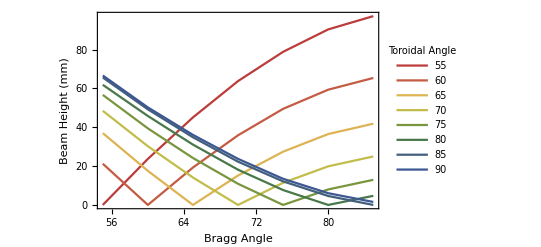

```mathematica
ListPlot[Labelled,PlotLegends->LineLegend[TAngs,LegendLabel->"Toroidal Angle"],Joined->True,Frame->True,FrameLabel->{"Bragg Angle", "Beam Height (mm)"},LabelStyle->16,PlotStyle->Colors[Length[Labelled]]]
```

```mathematica
Export["HeightPlot.png",%];
```

```mathematica
Keys[plots]
```

Keys::invrl: The argument plots is not a valid Association or a list of rules.

Keys[plots]

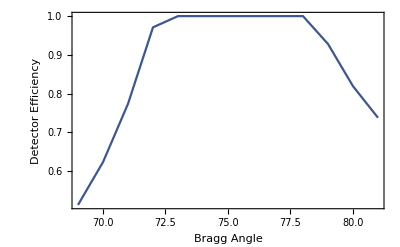

```mathematica
t = Table[detectorFraction[75 Degree, bragg Degree]//N,{bragg,69,81,1}];
BAngs = Range[69,81,1];
Labelled = Transpose[{BAngs,t}];
ListPlot[Labelled,Joined->True,Frame->True,FrameLabel->{"Bragg Angle", "Detector Efficiency"},LabelStyle->16,PlotStyle->Colors[Length[Labelled]]]
```

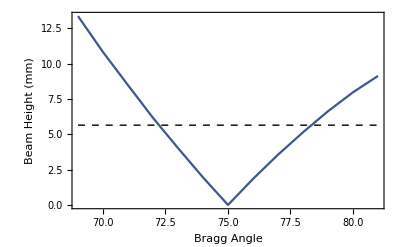

```mathematica
t = Table[heights[75 Degree, bragg Degree]/mm//N,{bragg,69,81,1}];
BAngs = Range[69,81,1];
Labelled = Transpose[{BAngs,t}];
ListPlot[Labelled,Joined->True,Frame->True,FrameLabel->{"Bragg Angle", "Beam Height (mm)"},LabelStyle->16,PlotStyle->Colors[Length[Labelled]],Epilog->{Dashed,Line[{{69,5.64 },{81,5.64}}]}]
```

```mathematica
(25/Pi)^0.5*2
```

5.6419

$Aborted